Philippe Morel
UCL Bartlett “Skills Module”
Mathematica FINAL EXAM
Academic Year 2019-2020
February 20, 2020


You have 3 hours
GOOD LUCK !

Exercise 1
Could you, in one line, explain what are the following ideas/concepts
(directly write between the questions by adding new lines - like where there are the “XXXXXX” - with a different text color)

a- What is a constant ?
a certain value that once has been defined will never change again. such as Pi
b- What is a variable ?
a value that can change according to some other change. we can define it and change it at any time. normally relative to a function. 

c- How do you create a constant in Mathematica?
just define a value that never have relation with any variable. Such as “a = - E”

d- How can you make immediately the difference between a constant you create and one that is part of the MMA system (a native one), just by looking at its name (at its symbol) without any need for evaluation ?
use function “Information”. If it is a native constant, such as “Information[E]”it will give some detailed information. If it is a constant defined by me, such as “a = - E; Information[a]”, it will not give a introduction.

e- Which “equality like” signs allow you to implement in MMA these 2 different concepts of constant and variable?
=

f- Once you have assigned a value to something, how can you remove or kill this value?
Clear

g- can you write 5 function shortcuts making use of the sign “=”
ReplaceAll                 /.
ReplaceRepeated  //.
map                            /@
the last value         %
condition                /;
apply                        @@



h- What is a list?
a set of value(element). a sequence of value(element).


i- What is an index?
the position of element in a list.


j- Can you explain the difference between 3 types of use of squares brackets ?
1. use in function:      f[x]
2.extract element from a list:    {a, b, c, d, e, f}[[2 ]]
3.the number of squares brackets represents the layer of function.



k- Explain the difference between 3 types of brackets (standard, curly, square)?
():  1+(2/3)          use in calculation
[]:  f[x]                  use in function
{}:{1,2,3,4,5}      use in list


l- What are (or not) the differences between a “scalar”, a “vector”, a “list”,  a “matrix” ?
A scalar is a a non-listed value.  like  k
A vector is a list of non-list elements. like      v = {1, 2.3, x + 4};
A matrix is a list of vectors of equal length, like  m = {{1, 2, 3}, {1, 4, 9}};
vector and matrix belong to list. list include matrix, vector and other strcuture of data.

m- Can you give examples of 5 differently structured lists?
{a}
{a,b,c}
{{a,b},{c,d}}
{a,b,c,{d,e}}
{{a,b},{c,d},{e,{f,g,h}}}


n- What does “listable” mean ?
Listable is a property that can be assigned a symbol to specify that the function automatically linearly acts on the list that appears as its argument.


o- Can you give 5 examples of built-in MMA functions that are “listable” ?
Log[{a, b, c}]
{a,b,c}+1
{a,b,c}/2
{a, b, c}^5
Sqrt[{a,b,c}]


p- To which element you should pay attention to when using function like TreeForm, or MatrixForm, etc.?
depth and demention


q- what is “@” and “//”
@ is used to replace [].   f@x
// is reverse to @.      x//f


r- what is “/@” and “@@”
/@ replace map.      @@ replace apply
-Graphics-

s- How can you make the difference in MMA between creating local and global variables?
use Module or Block to create local variable.


t- What is an iteration, and an iterator ?
iteration:the repeated application of a transformation.
iterator: function used for iteration. such as Foldlist, Table and complex function defined by coder.


u- What does recursion means ?
A recursive process is one in which objects are defined in terms of other objects of the same type. Using some sort of recurrence relation, the entire class of objects can then be built up from a few initial values and a small number of rules. The Fibonacci numbers are most commonly defined recursively.


v- How can you easily increment or decrement values in MMA ? Give at least 2 differents examples of doing it for each ?
increment:    Table[RandomInteger[], 20]        Range[1,50,0.2]
decrement:    Most[{a, b, c, d}],     Take[{a, b, c, d, e, f}, {1, -1, 2}]

Exercise 2
Try to predict the result of the following 3 expressions without evaluating them

```mathematica
For[{i=1,j=0},i<=20030,i=i+1,j=j+i];j
```

200610465

```mathematica
Sum[k,{k,1,20030}]
```

200610465

```mathematica
Apply[Plus,Range[20030]]
```

200610465

Now evaluate the above cells, and propose at least 4 new expressions that allow you to obtain the same result, without using “For”, “Sum” or “Apply”

#### 1.

```mathematica
Total[Range[20030]]
```

200610465

#### 2.

```mathematica
Fold[Plus,Range[20030]]
```

200610465

#### 3.

```mathematica
n=1;m=0;
While[n<20031,{m=m+n,n++}];
Print[m]
```

200610465

#### 4.

```mathematica
m=0;
Do[m=m+n,{n,20030}]
Print[m]
```

200610465

#### 5. fail

```mathematica
Plus#&/@(Sequence[Range[20]])
```

{Plus,2 Plus,3 Plus,4 Plus,5 Plus,6 Plus,7 Plus,8 Plus,9 Plus,10 Plus,11 Plus,12 Plus,13 Plus,14 Plus,15 Plus,16 Plus,17 Plus,18 Plus,19 Plus,20 Plus}

#### 6.use fixedpoint, has some problem when the length of list is odd

```mathematica
kkk[x_]:=Partition[Range[x],2]
```

```mathematica
kkk[20]
```

{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20}}

```mathematica
Plus[kkk[20][[1,1]],kkk[20][[1,2]]]
```

3

```mathematica
Table[Plus[kkk[20][[t,1]],kkk[20][[t,2]]],{t,1,10}]
```

{3,7,11,15,19,23,27,31,35,39}

```mathematica
jjj[x_]:=Table[Plus[kkk[x][[t,1]],kkk[x][[t,2]]],{t,1,x/2}]
```

```mathematica
jjj[20]
```

{3,7,11,15,19,23,27,31,35,39}

```mathematica
iii[x_]:=Table[Plus[Partition[x,2][[t,1]],Partition[x,2][[t,2]]],{t,1,Length[x]/2}]
```

```mathematica
iii[Range[20]]
```

{3,7,11,15,19,23,27,31,35,39}

```mathematica
NestList[iii,Range[20],2]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{3,7,11,15,19,23,27,31,35,39},{10,26,42,58,74}}

```mathematica
FixedPointList[iii,Range[20]]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{3,7,11,15,19,23,27,31,35,39},{10,26,42,58,74},{36,100},{136},{},{}}

```mathematica
FixedPointList[iii,Range[20]][[-3]]
```

{136}

```mathematica
FixedPointList[iii,Range[20030]][[-3]]
```

{134225920}

#### 7.

```mathematica
20030*(20030+1)/2
```

200610465

```mathematica
Last[NestList[#*(#+1)/2&,20030,1]]
```

200610465

```mathematica
Nest[#*(#+1)/2&,20030,1]
```

200610465

Exercise 3
Do the same by making use of at least one pure function
Also explain what is the main advantage in using pure function (at least one advantage)

#### 1.

```mathematica
Total[#]&[Range[20030]]
```

200610465

#### 2.

```mathematica
Fold[Plus,#]&[Range[20030]]
```

200610465

#### 3.

```mathematica
n=1;m=0;
While[n<20031,{m=m+n,n++}];
Print[#]&[m]
```

200610465

Exercise 4
Create a function that:
- Create a square, with a circle inside, with a square inside the circle, with a circle inside this new square, etc.
constrain 1: The circles should have random centers and radii, but they should never go beyond the limits of the squares
constrain 2:The squares should have exactly the size of the circles

Choose the number of iterations (or recursions) you want, and compute the following total areas after a certain amount of iterations :
- Total area of all the squares
- Total area of all the circles

```mathematica
cp0={0,0};
a0={-10,-10};
b0={10,10};
CCC[{a_,b_},r_]:=Graphics[{Circle[{a,b},r]}]
RRR[{a_,b_},{c_,d_}]:=Graphics[{Opacity[0],EdgeForm[Thin],FaceForm[White],Rectangle[{a,b},{c,d}]}]
R0=RRR[a0,b0];
show[a___]:=Show[a,Frame->True,PlotRange->{{-15,15},{-15,15}}]
```

{9.28512,-9.25124}

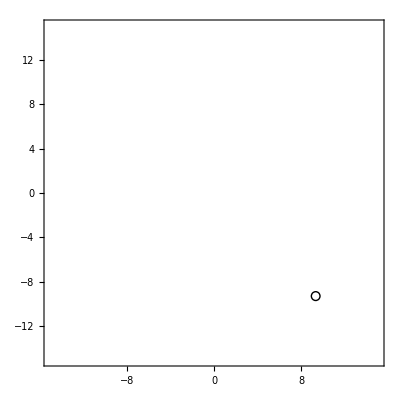

```mathematica
cp1a=RandomReal[{a0[[1]],b0[[1]]}];
cp1b=RandomReal[{a0[[2]],b0[[2]]}];
cp1={cp1a,cp1b}
Abs[Flatten[{cp1-a0,cp1-b0}]];
k1=Min[Abs[Flatten[{cp1-a0,cp1-b0}]]];
r1=RandomReal[{k1/2,k1}];
C1=CCC[cp1,r1];
show[R0,C1]
```

```mathematica
a1=cp1-r1*(Sqrt[2]/2);
b1=cp1+r1*(Sqrt[2]/2);
R1=RRR[a1,b1];
show[R0,C1,R1]
```

-Graphics-

{9.25461,-9.34441}

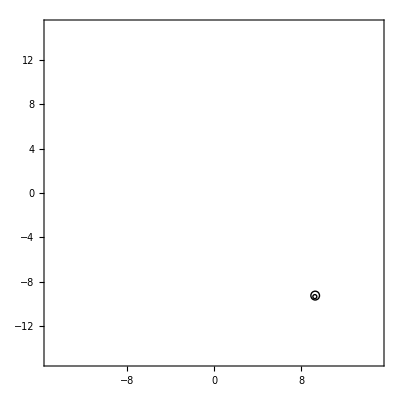

```mathematica
cp2a=RandomReal[{a1[[1]],b1[[1]]}];
cp2b=RandomReal[{a1[[2]],b1[[2]]}];
cp2={cp2a,cp2b}
Abs[Flatten[{cp2-a1,cp2-b1}]];
k2=Min[Abs[Flatten[{cp2-a1,cp2-b1}]]];
r2=RandomReal[{k2/2,k2}];
C2=CCC[cp2,r2];
show[R0,C1,R1,C2]
```

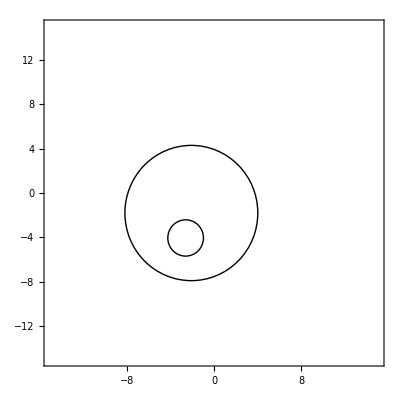

```mathematica
cp1a=RandomReal[{a0[[1]],b0[[1]]}];
cp1b=RandomReal[{a0[[2]],b0[[2]]}];
cp1={cp1a,cp1b};
Abs[Flatten[{cp1-a0,cp1-b0}]];
k1=Min[Abs[Flatten[{cp1-a0,cp1-b0}]]];
r1=RandomReal[{k1/2,k1}];
C1=CCC[cp1,r1];
a1=cp1-r1*(Sqrt[2]/2);
b1=cp1+r1*(Sqrt[2]/2);
R1=RRR[a1,b1];
cp2a=RandomReal[{a1[[1]],b1[[1]]}];
cp2b=RandomReal[{a1[[2]],b1[[2]]}];
cp2={cp2a,cp2b};
Abs[Flatten[{cp2-a1,cp2-b1}]];
k2=Min[Abs[Flatten[{cp2-a1,cp2-b1}]]];
r2=RandomReal[{k2/2,k2}];
C2=CCC[cp2,r2];
show[R0,C1,R1,C2]
```

```mathematica
areaOfRec=(a0-b0)[[1]]*(a0-b0)[[2]]+(a1-b1)[[1]]*(a1-b1)[[2]]
```

404.138

```mathematica
areaOfCir=Pi(r1^2+r2^2)
```

6.5362

Exercise 5
Take the function you just created, and:
- throw GREEN random points in the circles
- throw BLUE random points in the regions between the limits of the circles and the squares
- Make the size of the point dependant of their distances from the centers of the circles

```mathematica
x=RandomReal[{a0[[1]],b0[[1]]},10];
y=RandomReal[{a0[[2]],b0[[2]]},10];
pointList=Transpose[{x,y}]
```

{{3.93744,3.18362},{4.24955,-3.2073},{-4.94887,6.97854},{-7.81921,-7.34748},{-4.25907,-0.636365},{-2.89609,7.8787},{-6.6139,8.09573},{-4.98701,-5.76912},{0.600242,-5.6026},{-9.18864,5.67374}}

```mathematica
EuclideanDistance[#,cp1]&/@pointList
```

{4.61153,10.9676,9.51258,19.5111,12.1541,7.42892,11.1509,16.5395,13.9258,13.8777}

```mathematica
r1
```

1.43837

```mathematica
#<r1&/@(EuclideanDistance[#,cp1]&/@pointList)
```

{False,False,False,False,False,False,False,False,False,False}

```mathematica
ptInCir=Pick[pointList,#<r1&/@(EuclideanDistance[#,cp1]&/@pointList)]
```

{}

```mathematica
x=RandomReal[{a0[[1]],b0[[1]]},1000];
y=RandomReal[{a0[[2]],b0[[2]]},1000];
pointList=Transpose[{x,y}];
ptInCir=Pick[pointList,#<r1&/@(EuclideanDistance[#,cp1]&/@pointList)];
ptInRec=Pick[pointList,Table[pointList[[t,1]]>a0[[1]]&&pointList[[t,1]]<b0[[1]]&&pointList[[t,2]]>a0[[2]]&&pointList[[t,2]]<b0[[2]],{t,1000}]];
ptBet=Pick[ptInRec,!#<r1&/@(EuclideanDistance[#,cp1]&/@pointList)];
P1=Graphics[{Green,Point[ptInCir]}];
P2=Graphics[{Blue,Point[ptBet]}];
```

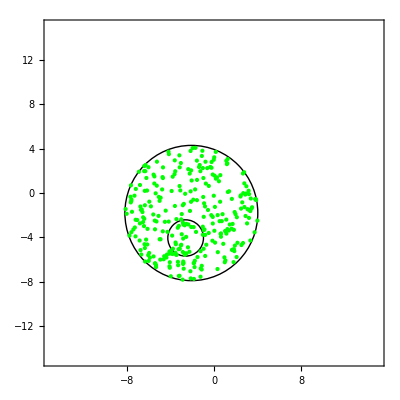

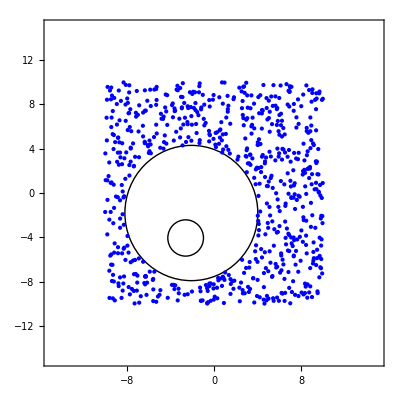

```mathematica
show[R0,C1,R1,C2,P1]
show[R0,C1,R1,C2,P2]
```

```mathematica
AA=EuclideanDistance[#,cp1]&/@ptInCir
```

{5.95741,4.85424,1.47735,1.9937,2.40235,5.63764,1.82482,3.54443,1.91686,6.00886,5.59069,1.1661,5.16393,3.98601,2.18139,3.86612,4.88276,5.34987,3.98153,5.74396,1.09232,2.64971,4.50496,5.62463,1.216,4.31152,1.26676,5.74565,6.07883,6.07849,4.85942,3.07193,5.23478,2.42242,2.27518,1.62114,5.79064,4.44132,5.90377,3.55925,3.25883,5.56739,4.19119,2.69198,2.21863,3.39934,5.00459,4.50592,5.00973,4.32819,4.04513,4.80399,4.18607,5.30644,1.26335,4.47863,1.82097,1.08571,4.28319,5.92569,4.07431,5.33325,5.42659,2.82929,1.63429,4.30339,1.46184,1.01367,2.68694,4.86867,5.54167,3.91431,3.82412,3.428,4.89919,3.11652,0.228734,3.66835,4.25752,5.63338,3.82941,5.44586,3.1065,5.08783,4.01599,3.09806,4.39411,2.6638,3.02239,5.61709,4.01103,4.61815,4.26904,5.01964,5.77918,1.25962,5.35632,0.887929,3.78524,5.22321,5.29738,5.22764,4.79242,4.18675,5.41319,3.60467,5.52883,3.1721,5.14774,4.99411,1.95517,6.0621,5.61012,3.42235,1.26439,3.72354,2.55725,5.44977,5.59677,5.44801,3.96498,3.44451,3.49811,3.15428,4.20912,5.3172,1.83904,4.75121,6.08515,3.84604,4.95734,5.39564,4.88563,2.86444,6.0514,5.03104,4.36502,3.84906,3.03019,6.03409,3.76095,4.35024,5.94713,5.07094,1.05227,4.74835,4.56377,1.07427,5.88514,5.5625,2.41857,3.99248,3.46583,5.19807,4.98605,2.92026,4.57126,4.05292,3.66442,4.98262,5.70348,3.28596,5.48364,5.88778,2.69422,3.27396,4.49712,4.60895,3.84993,5.45886,4.81104,3.6777,5.2052,5.07732,5.7019,2.88601,5.89942,5.06949,3.49509,2.23174,3.61409,1.06756,1.286,3.49525,3.02935,5.93327,5.22512,3.69768,3.95361,5.5983,2.58217,5.98826,5.30698,6.09624,4.01082,5.70053,5.66366,4.73084,4.18079,5.60501,5.34493,2.36571,2.76755,5.54056,1.55099,1.75778,4.85969,3.64513,2.15722,1.81127,6.03355,4.32289,5.25213,5.64034,3.13724,5.77061,4.95728,3.98521,6.0955,4.65086,4.31466,5.28869,4.90071,4.57884,5.27929,4.03845,3.81693,2.34443,5.52921,2.93349,3.97806,2.97044,6.05722,5.76582,2.10746,3.3411,2.22852,4.62298,4.52228,5.18111,3.92771,5.62664,5.23016,5.48058,5.80668,6.05835,2.20357,5.72231,3.41407,4.71472,4.09317,5.85667,3.32178,1.63701,3.68587,3.63412,1.18576,4.94059,5.54926,5.91288,4.44071,4.80802,5.92352,5.69585,5.8228,5.54161,5.13615,5.08819,4.63203,3.83201,6.04623,4.72156,3.15891,3.28823,4.488,3.97475,4.50398,5.31589,6.05458,3.71371,3.01013,5.73988,3.86307,5.59571,3.75,3.99905,5.84812,4.76857,4.08799,5.95139,1.38879,4.56172,1.90809,4.54134,5.19713,3.45702,4.17549,4.01743}

Exercise 6
What could be the figure below?
- Try to replicate it (any manner) by writing your own functions
- Try to understand the rule (the logic) that might be hidden in this graphics
- Just write down this rule “by hand” (I mean just write and explain)
 - Try to recreate this figure by making use of the rule you might have found

-Graphics-

```mathematica
l1={{0,0,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0},{1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,1,0,0,0,1,1}}
MatrixPlot[l1,ColorFunction->"Monochrome" ,MeshStyle->Gray,Mesh->True,ImageSize->Medium]
```

{{0,0,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0},{1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,1,0,0,0,1,1}}

-Graphics-